# 5. NALOGA: ŽELVA

## REŠITEV

```mathematica
Nkorakov=1234;
Nposkusov=12345;
Δφmax=12°;


φjiji=Accumulate[
	RandomReal[{-Δφmax,Δφmax},{Nkorakov,Nposkusov}]
]ᵀ;

rjiKončni=Total[{Sin@φjiji,Cos@φjiji},{3}]ᵀ;
10^2 Round[Mean[Norm/@rjiKončni]/10^2]
```

500

## ZA PREDSTAVO

Tako nekako zgledajo poti:

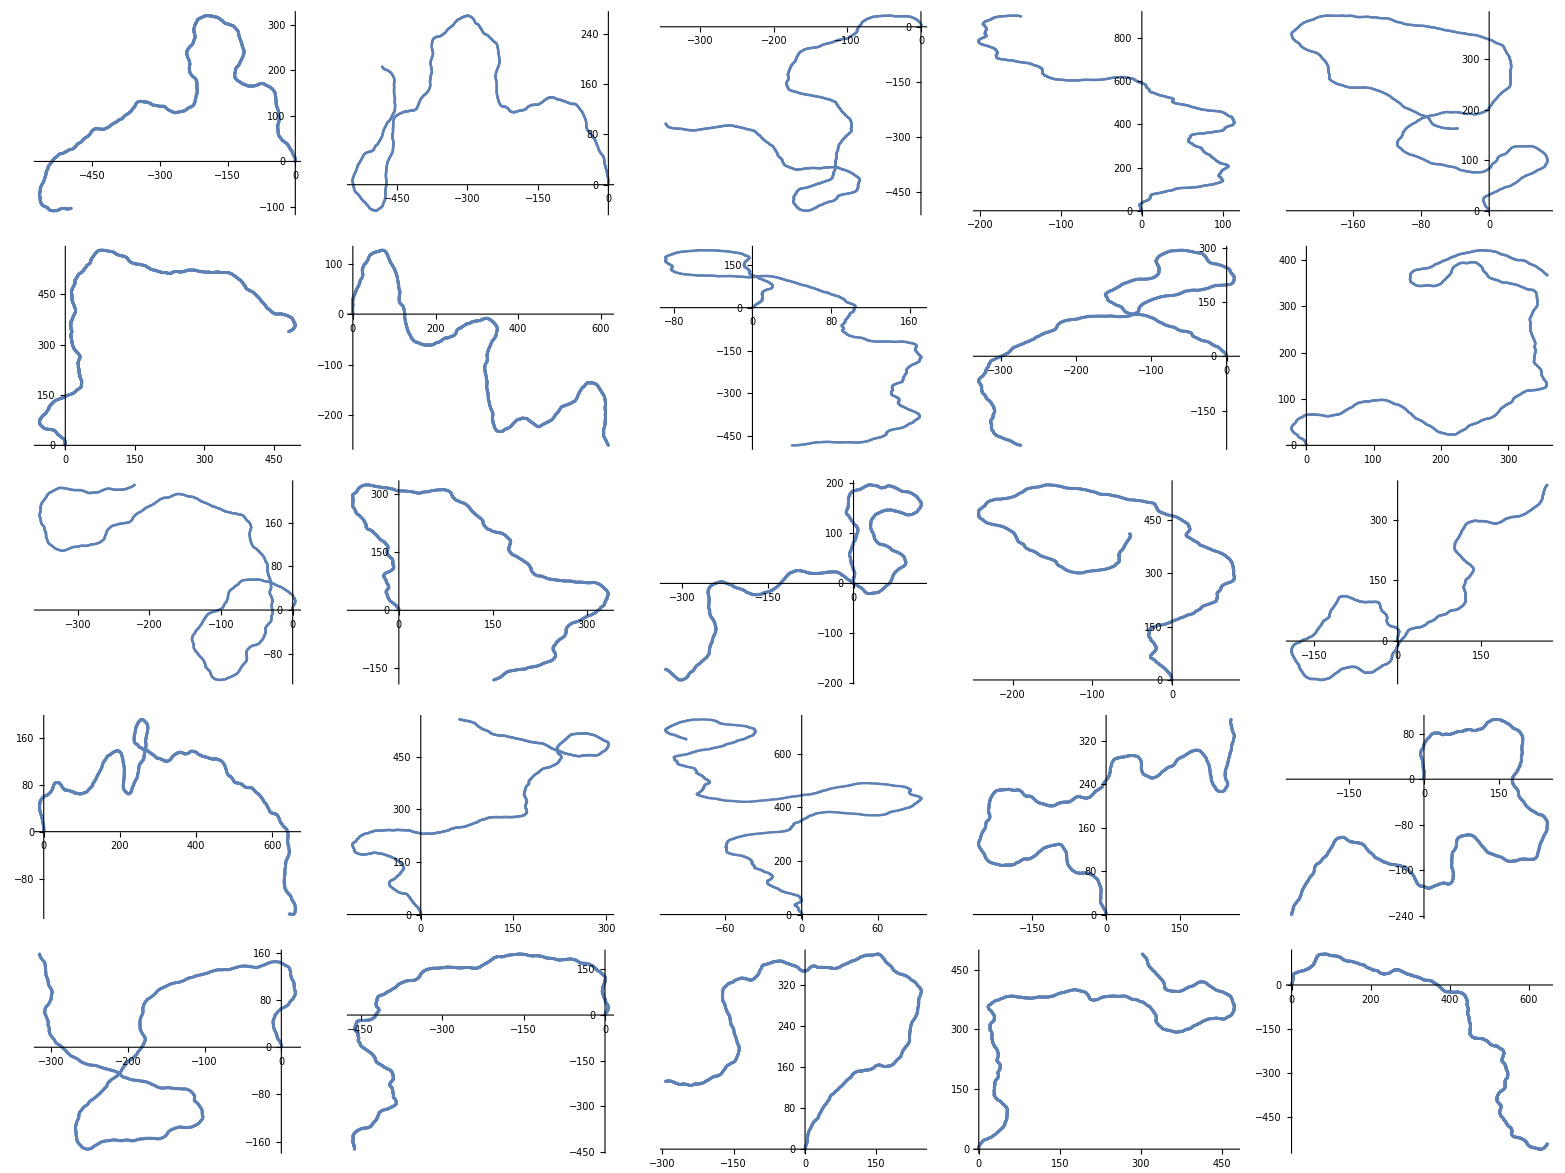

```mathematica
Grid[ArrayReshape[
	ParallelMap[
		ListPlot,
		Transpose[
			ParallelMap[Accumulate,{Sin@φjiji,Cos@φjiji},{2}],
			InversePermutation@{2,3,1}
		][[;;25]]	
	],
	{5,5}
],Frame->All]
```